```mathematica
{triangle,square,dualsquare,dualsquaresplit,dualsquaresplitsplit,dualsquaresplitdual,full}
```

```mathematica
split triangle -> (1, 2, 3 )*2 triangles
split square -> 2*2 triangle
split dualsquare -> dualsquaresplit
split dualsquaresplit ->dualsquaresplitsplit or 0
split dualsquaresplitsplit -> fail
split dualsquaresplitdual -> full
```

```mathematica
dual triangle->4 triangles
dual square ->dualsquare & 4 triangles
dual dualsquare ->dualsquare & 4 triangles
dual dualsquaresplit-> dualsquaresplitdual 
dual dualsquaresplitsplit->full
dual dualsquaresplitdual
```

```mathematica
split[triangle]={1,0,0,0,0,0,0}
split[square]={0,0,0,0,0,0,0}
split[dualsquare]={4,0,-1,1,0,0,0}
split[dualsquareplit]={2,0,0,-1,1,0,0}||{0,0,0,0,0,0,0}||{0,0,0,0,0,0,0}
split[dualsquaresplitsplit]={0,0,0,0,0,0,0}
split[dualsquaresplitdual]={4,0,0,0,0,-1,1}||{0,0,0,0,0,0,0}||{0,0,0,0,0,0,0}
```

```mathematica
dual[triangle]={3,0,0,0,0,0,0}
dual[square]={4,-1,1,0,0,0,0}
dual[dualsquare]={4,0,0,0,0,0,0}
dual[dualsquaresplit]={0,0,0,-1,0,1,0}
dual[dualsquaresplitsplit]={4,0,0,0,-1,0,1}
dual[dualsquaresplitdual]={0,0,0,0,0,0,0}
```

```mathematica
probability p of split
probability (1-p) of dual
```

```mathematica
branch[{a,b,c,d,e,f,g}]
(a*p)/(a+b+c+d+e+f)->list+{1,0,0,0,0,0,0}
(b*p)/(a+b+c+d+e+f)->list+{0,0,0,0,0,0,0}
(c*p)/(a+b+c+d+e+f)->list+{4,0,-1,1,0,0,0}
(d*p/3)/(a+b+c+d+e+f)->list+{2,0,0,-1,1,0,0}
(2d*p/3)/(a+b+c+d+e+f)->list+{0,0,0,0,0,0,0}
(e*p)/(a+b+c+d+e+f)->list+{0,0,0,0,0,0,0}
(f*p/3)/(a+b+c+d+e+f)->list+{4,0,0,0,0,-1,1}
(2f*p/3)/(a+b+c+d+e+f)->list+{0,0,0,0,0,0,0}
(a*(1-p))/(a+b+c+d+e+f)->list+{3,0,0,0,0,0,0}
(b*(1-p))/(a+b+c+d+e+f)->list+{4,-1,1,0,0,0,0}
(c*(1-p))/(a+b+c+d+e+f)->list+{4,0,0,0,0,0,0}
(d*(1-p))/(a+b+c+d+e+f)->list+{0,0,0,-1,0,1,0}
(e*(1-p))/(a+b+c+d+e+f)->list+{4,0,0,0,-1,0,1}
(f*(1-p))/(a+b+c+d+e+f)->list+{0,0,0,0,0,0,0}
```

```mathematica
list->
```

```mathematica
n2int[
```

```mathematica
even->%/2
odd->(1-%)/2
```

```mathematica
Pair[{x_,y_}]:=(x^2+3x+2 x y+y+y^2)/2
Unpair[z_]:=With[{i=Floor[(-1+√(1+8z))/2]},{z-(i(1+i))/2,(i(3+i))/2-z}]
Pair[{2,2}]
Unpair[%]
```

12

{2,2}

```mathematica
u1[z_]:=z-(Floor[(-1+√(1+8z))/2](1+Floor[(-1+√(1+8z))/2]))/2
u2[z_]:=(Floor[(-1+√(1+8z))/2](3+Floor[(-1+√(1+8z))/2]))/2-z
```

```mathematica
sfold[{a_,b_,c_,d_,e_,f_,g_}]:=Pair[{Pair[{a,Pair[{b,c}]}],Pair[{Pair[{d,e}],Pair[{f,g}]}]}]
p[p[a,p[b,c]],p[p[d,e],p[f,g]]]
{u1[z],u2[z]}
{u1[u1[z]],u1[u2[u1[z]]],u2[u2[u1[z]]],u1[u1[u2[z]]],u2[u1[u2[z]]],u1[u2[u2[z]]],u2[u2[u2[z]]]}
```

```mathematica
fol[{a_,b_,c_,d_,e_,f_,g_}]:=p[p[a,p[b,c]],p[p[d,e],p[f,g]]]
```

```mathematica
p[x_,y_]:=(x^2+3x+2 x y+y+y^2)/2
```

```mathematica
{u1[u1[z]],u1[u2[u1[z]]],u2[u2[u1[z]]],u1[u1[u2[z]]],u2[u1[u2[z]]],u1[u2[u2[z]]],u2[u2[u2[z]]]}+{1,0,0,0,0,0,0}
{u1[u1[z]],u1[u2[u1[z]]],u2[u2[u1[z]]],u1[u1[u2[z]]],u2[u1[u2[z]]],u1[u2[u2[z]]],u2[u2[u2[z]]]}+{4,0,-1,1,0,0,0}
{u1[u1[z]],u1[u2[u1[z]]],u2[u2[u1[z]]],u1[u1[u2[z]]],u2[u1[u2[z]]],u1[u2[u2[z]]],u2[u2[u2[z]]]}+{2,0,0,-1,1,0,0}
list+{4,0,0,0,0,-1,1}
list+{3,0,0,0,0,0,0}
list+{4,-1,1,0,0,0,0}
list+{4,0,0,0,0,0,0}
list+{0,0,0,-1,0,1,0}
list+{4,0,0,0,-1,0,1}
```

```mathematica
{{(a*p)/(a+b+c+d+e+f),{z,fol[{a+1,b,c,d,e,f,g}]}},
{(c*p)/(a+b+c+d+e+f),{z,fol[{a+4,b,c-1,d+1,e,f,g}]}},
{(d*p/3)/(a+b+c+d+e+f),{z,fol[{a+2,b,c,d-1,e+1,f,g}]}},
{(f*p/3)/(a+b+c+d+e+f),{z,fol[{a+4,b,c,d,e,f-1,g+1}]}},
{(a*(1-p))/(a+b+c+d+e+f),{z,fol[{a+3,b,c,d,e,f,g}]}},
{(b*(1-p))/(a+b+c+d+e+f),{z,fol[{a+4,b-1,c+1,d,e,f,g}]}},
{(c*(1-p))/(a+b+c+d+e+f),{z,fol[{a+4,b,c,d,e,f,g}]}},
{(d*(1-p))/(a+b+c+d+e+f),{z,fol[{a,b,c,d-1,e,f+1,g}]}},
{(e*(1-p))/(a+b+c+d+e+f),{z,fol[{a+4,b,c,d,e-1,f,g+1}]}},
{(-f (-3+p)+(3 b+2 d+3 e) p)/(3 (a+b+c+d+e+f)),{z,z}}}/.{a->u1[u1[z]],b->u1[u2[u1[z]]],c->u2[u2[u1[z]]],d->u1[u1[u2[z]]],e->u2[u1[u2[z]]],f->u1[u2[u2[z]]],g->u2[u2[u2[z]]]}
```

```mathematica
{{(p u1[u1[z]])/(u1[u1[z]]+u1[u1[u2[z]]]+u1[u2[u1[z]]]+u1[u2[u2[z]]]+u2[u1[u2[z]]]+u2[u2[u1[z]]]),{z,p[p[1+u1[u1[z]],p[u1[u2[u1[z]]],u2[u2[u1[z]]]]],p[p[u1[u1[u2[z]]],u2[u1[u2[z]]]],p[u1[u2[u2[z]]],u2[u2[u2[z]]]]]]}},{(p u2[u2[u1[z]]])/(u1[u1[z]]+u1[u1[u2[z]]]+u1[u2[u1[z]]]+u1[u2[u2[z]]]+u2[u1[u2[z]]]+u2[u2[u1[z]]]),{z,p[p[4+u1[u1[z]],p[u1[u2[u1[z]]],-1+u2[u2[u1[z]]]]],p[p[1+u1[u1[u2[z]]],u2[u1[u2[z]]]],p[u1[u2[u2[z]]],u2[u2[u2[z]]]]]]}},{(p u1[u1[u2[z]]])/(3 (u1[u1[z]]+u1[u1[u2[z]]]+u1[u2[u1[z]]]+u1[u2[u2[z]]]+u2[u1[u2[z]]]+u2[u2[u1[z]]])),{z,p[p[2+u1[u1[z]],p[u1[u2[u1[z]]],u2[u2[u1[z]]]]],p[p[-1+u1[u1[u2[z]]],1+u2[u1[u2[z]]]],p[u1[u2[u2[z]]],u2[u2[u2[z]]]]]]}},{(p u1[u2[u2[z]]])/(3 (u1[u1[z]]+u1[u1[u2[z]]]+u1[u2[u1[z]]]+u1[u2[u2[z]]]+u2[u1[u2[z]]]+u2[u2[u1[z]]])),{z,p[p[4+u1[u1[z]],p[u1[u2[u1[z]]],u2[u2[u1[z]]]]],p[p[u1[u1[u2[z]]],u2[u1[u2[z]]]],p[-1+u1[u2[u2[z]]],1+u2[u2[u2[z]]]]]]}},{((1-p) u1[u1[z]])/(u1[u1[z]]+u1[u1[u2[z]]]+u1[u2[u1[z]]]+u1[u2[u2[z]]]+u2[u1[u2[z]]]+u2[u2[u1[z]]]),{z,p[p[3+u1[u1[z]],p[u1[u2[u1[z]]],u2[u2[u1[z]]]]],p[p[u1[u1[u2[z]]],u2[u1[u2[z]]]],p[u1[u2[u2[z]]],u2[u2[u2[z]]]]]]}},{((1-p) u1[u2[u1[z]]])/(u1[u1[z]]+u1[u1[u2[z]]]+u1[u2[u1[z]]]+u1[u2[u2[z]]]+u2[u1[u2[z]]]+u2[u2[u1[z]]]),{z,p[p[4+u1[u1[z]],p[-1+u1[u2[u1[z]]],1+u2[u2[u1[z]]]]],p[p[u1[u1[u2[z]]],u2[u1[u2[z]]]],p[u1[u2[u2[z]]],u2[u2[u2[z]]]]]]}},{((1-p) u2[u2[u1[z]]])/(u1[u1[z]]+u1[u1[u2[z]]]+u1[u2[u1[z]]]+u1[u2[u2[z]]]+u2[u1[u2[z]]]+u2[u2[u1[z]]]),{z,p[p[4+u1[u1[z]],p[u1[u2[u1[z]]],u2[u2[u1[z]]]]],p[p[u1[u1[u2[z]]],u2[u1[u2[z]]]],p[u1[u2[u2[z]]],u2[u2[u2[z]]]]]]}},{((1-p) u1[u1[u2[z]]])/(u1[u1[z]]+u1[u1[u2[z]]]+u1[u2[u1[z]]]+u1[u2[u2[z]]]+u2[u1[u2[z]]]+u2[u2[u1[z]]]),{z,p[p[u1[u1[z]],p[u1[u2[u1[z]]],u2[u2[u1[z]]]]],p[p[-1+u1[u1[u2[z]]],u2[u1[u2[z]]]],p[1+u1[u2[u2[z]]],u2[u2[u2[z]]]]]]}},{((1-p) u2[u1[u2[z]]])/(u1[u1[z]]+u1[u1[u2[z]]]+u1[u2[u1[z]]]+u1[u2[u2[z]]]+u2[u1[u2[z]]]+u2[u2[u1[z]]]),{z,p[p[4+u1[u1[z]],p[u1[u2[u1[z]]],u2[u2[u1[z]]]]],p[p[u1[u1[u2[z]]],-1+u2[u1[u2[z]]]],p[u1[u2[u2[z]]],1+u2[u2[u2[z]]]]]]}},{(-(-3+p) u1[u2[u2[z]]]+p (2 u1[u1[u2[z]]]+3 u1[u2[u1[z]]]+3 u2[u1[u2[z]]]))/(3 (u1[u1[z]]+u1[u1[u2[z]]]+u1[u2[u1[z]]]+u1[u2[u2[z]]]+u2[u1[u2[z]]]+u2[u2[u1[z]]])),{z,z}}}
```

{{(p (z-1/2 Floor[1/2 (-1+√(1+8 z))] (1+Floor[1/2 (-1+√(1+8 z))])-1/2 Floor[1/2 (-1+√(1+8 (z-1/2 Floor[1/2 (-1+√(1+8 z))] (1+Floor[1/2 (-1+√(1+8 z))]))))] (1+Floor[1/2 (-1+√(1+8 (z-1/2 Floor[1/2 (-1+√(1+8 z))] (1+Floor[1/2 (-1+√(1+8 z))]))))])))/1,{z,1/2 (3/2 (3 (1+z-1/2 Floor[1/2 (-1+√(1+8 z))] (1+Floor[1/2 (-1+√(1+8 z))])-1/2 Floor[1/2 (-1+√(1+8 (z-1/2 Floor[1/2 (-1+√(1+8 z))] (1+Floor[1/2 (-1+√(1+8 z))]))))] (1+Floor[1/2 (-1+√(1+8 (z-1/2 Floor[1/2 (-1+√(1+8 z))] (1+Floor[1/2 (-1+√(1+8 z))]))))]))+3+1/4 (9+(1)^2)^2)+1/4 (1)^2+1+1/2 (1) (1)+1/4 (3/2 (1)+3+1)^2)}},8,{1,1}}
 |  |  |  |

```mathematica
SparseArray
```

```mathematica
{a,b,c,d,e,f,g}
(-f (-3+p)+(3 b+2 d+3 e) p)/(3 (a+b+c+d+e+f))
```

```mathematica
(b*p)/(a+b+c+d+e+f)+(2d*p/3)/(a+b+c+d+e+f)+(e*p)/(a+b+c+d+e+f)+(2f*p/3)/(a+b+c+d+e+f)+(f*(1-p))/(a+b+c+d+e+f)
```

```mathematica
Simplify[(b*p)/(a+b+c+d+e+f)+(2d*p/3)/(a+b+c+d+e+f)+(e*p)/(a+b+c+d+e+f)+(2f*p/3)/(a+b+c+d+e+f)+(f*(1-p))/(a+b+c+d+e+f)]
```

(-f (-3+p)+(3 b+2 d+3 e) p)/(3 (a+b+c+d+e+f))

```mathematica
(b[x+1]-b[x])/1==p[x]
b'[x]==p[x]
```

```mathematica
7t+d
a=t
b=1
c=2
d=3
e=4
f=5
g=0
```

```mathematica
sevenouts[z_]:=Sort[DeleteDuplicates[Block[{d=Mod[z,7],t=(z-Mod[z,7])/7},{
Boole[t>0](7 (1+t)+d),p/(t+1)
Boole[d==2](7 (4+t)+3),p/(t+1)
Boole[d==3](7 (2+t)+4),(p/3)/(t+1)
Boole[d==5](7 (4+t)),(p/3)/(t+1)
Boole[t>0](7 (3+t)+d),(1-p)/(t+1)
Boole[d==1](7 (4+t)+2),(1-p)/(t+1)
Boole[d==2](7 (4+t)+d),(1-p)/(t+1)
Boole[d==3](7 (0+t)+5),(1-p)/(t+1)
Boole[d==4](7 (4+t)),(1-p)/(t+1)
Boole[d==1](7t+6),p/(t+1)
Boole[d==3](7t+6),p/(t+1)
Boole[d==4](7t+6),p/(t+1)
Boole[d==5](7t+6),p/(t+1)
Boole[d==6](7t+6),(1-p)/(t+1)
```

```mathematica
t/2,t/2,1/2,1/2
```

```mathematica
{triangle,square,dualsquare,dualsquaresplit,dualsquaresplitsplit,dualsquaresplitdual,full,fail}
{t,1,2,3,4,5,0,6}
({{d[s], 1s, 2ds, 3dss, 4dsss, 5dssd, 0fu, 6fa}, {1s, 0, 0, 0, 0, 0, 0, 1/2}, {2ds, 0, (t/2)/(t+1), (1/2)/(t+1), 0, 0, 0, 0}, {3dss, 0, 0, (t/2)/(t+1), (1/6)/(t+1), 0, 0, (2/6)/(t+1)}, {4dsss, 0, 0, 0, (t/2)/(t+1), 0, 0, (1/2)/(t+1)}, {5dssd, 0, 0, 0, 0, (t/2)/(t+1), (1/3)/(t+1), (2/3)/(t+1)}, {0fu, 0, 0, 0, 0, 0, 1/2, 0}, {6fa, 0, 0, 0, 0, 0, 0, 1}})({{d[d], 1s, 2ds, 3dss, 4dsss, 5dssd, 0fu, 6fa}, {1s, 0, 1/2, 0, 0, 0, 0, 0}, {2ds, 0, (t/2+1/2)/(t+1), 0, 0, 0, 0, 0}, {3dss, 0, 0, (t/2)/(t+1), 0, (1/2)/(t+1), 0, 0}, {4dsss, 0, 0, 0, (t/2)/(t+1), 0, (1/2)/(t+1), 0}, {5dssd, 0, 0, 0, 0, (t/2)/(t+1), 0, 0}, {0fu, 0, 0, 0, 0, 0, 1/2, 0}, {6fa, 0, 0, 0, 0, 0, 0, 0}}) "probability of transition"
({{t[s], 1s, 2ds, 3dss, 4dsss, 5dssd, 0fu, 6fa}, {1s, 0, 0, 0, 0, 0, 0, 2}, {2ds, 0, 1, 0, 0, 0, 0, 0}, {3dss, 0, 0, 1, 2, 0, 0, 2}, {4dsss, 0, 0, 0, 1, 0, 0, 2}, {5dssd, 0, 0, 0, 0, 1, 2, 2}, {0fu, 0, 0, 0, 0, 0, 1, 0}, {6fa, 0, 0, 0, 0, 0, 0, 1}})({{t[d], 1s, 2ds, 3dss, 4dsss, 5dssd, 0fu, 6fa}, {1s, 0, 4, 0, 0, 0, 0, 0}, {2ds, 0, 4||3, 0, 0, 0, 0, 0}, {3dss, 0, 0, 3, 0, 4, 0, 0}, {4dsss, 0, 0, 0, 3, 0, 4, 0}, {5dssd, 0, 0, 0, 0, 3, 0, 0}, {0fu, 0, 0, 0, 0, 0, 3, 0}, {6fa, 0, 0, 0, 0, 0, 0, 0}})"triangles added by transition"
```

```mathematica
{a x+b,c x+d}
{e y+f,g y+h}
m1[i,k] m2[k,j]

a x+b==i
c x+d==k
e y+f==k
g y+h==j
```

```mathematica
LogicalExpand[Refine[Reduce[{7 x+b==i,7 x+d==k,7 y+b==k,7 y+d==j,b≥0,d≥0,i>0,j>0,k>0,x≥0,y≥0},Integers],{(a|b|c|d|i|j|k|x|y)∈Integers,a≥0,b≥0,c≥0,d≥0,i>0,j>0,k>0,x≥0,y≥0,(C[1]|C[2]|C[3]|C[4])∈Integers}]]
```

(C[1]+7 C[2]==b&&C[1]+7 C[3]==d&&1+C[2]+C[4]==x&&1+C[3]+C[4]==y&&7+C[1]+14 C[2]+7 C[4]==i&&7+C[1]+7 C[2]+7 C[3]+7 C[4]==k&&7+C[1]+14 C[3]+7 C[4]==j&&C[1]≥0&&C[2]≥0&&C[3]≥0&&C[4]≥0)||(1+C[1]+7 C[2]==b&&1+C[1]+7 C[3]==d&&C[2]+C[4]==x&&C[3]+C[4]==y&&1+C[1]+14 C[2]+7 C[4]==i&&1+C[1]+7 C[2]+7 C[3]+7 C[4]==k&&1+C[1]+14 C[3]+7 C[4]==j&&C[1]≥0&&C[2]≥0&&C[3]≥0&&C[4]≥0)

```mathematica
mult[{{b_,a_},{d_,c_}},{{f_,e_},{h_,g_}}]:=LogicalExpand[Refine[Reduce[{a x+b==i,c x+d==k,e y+f==k,g y+h==j,a≥0,b≥0,c≥0,d≥0,e≥0,f≥0,g≥0,h≥0,i>0,j>0,k>0,x≥0,y≥0},Integers],{(a|b|c|d|i|j|k|x|y)∈Integers,a≥0,b≥0,c≥0,d≥0,i>0,j>0,k>0,x≥0,y≥0}]]
mult[{{3,7},{10,7}},{{3,7},{10,7}}]
multfull[{{b_,a_},{d_,c_}},{{f_,e_},{h_,g_}}]:=Map[CoefficientList[#,C[1]]&,({i,j}/.Map[#[[2]]->#[[1]]&,Select[ToExpression[StringReplace[StringJoin["{{",ToString[mult[{{b,a},{d,c}},{{f,e},{h,g}}]],"}}"],{"&&"->"},{","=="->","}]],Length[#]>1&]])]
multfull[{{3,7},{10,7}},{{3,7},{10,7}}]
multfull[{{3,7},{10,7}},%]
multfull[{{3,7},{10,7}},%]
multfull[{{3,7},{10,7}},%]
(*multfull[%,%]
multfull[%,%]*)
```

C[1]∈Integers&&C[1]==x&&1+C[1]==y&&3+7 C[1]==i&&10+7 C[1]==k&&17+7 C[1]==j&&C[1]≥0

{{3,7},{17,7}}

{{3,7},{24,7}}

{{3,7},{31,7}}

{{3,7},{38,7}}

```mathematica
multfull[{{3,7},{10,7}},{{0,1},{0,1}}]
```

{{3,7},{10,7}}

```mathematica
{PadRight[CoefficientList[t,t],2],PadRight[CoefficientList[t,t],2]}
```

{{0,1},{0,1}}

```mathematica
q=21;
r=21;
Monitor[Block[{vlist=Map[{PadRight[CoefficientList[#[[1]],t],2],PadRight[CoefficientList[#[[2]],t],2]}&,Map[Expand,Map[First,{{{7t+1,7(t+4)+2},1/2},
{{7t+2,7(t+4)+2},1/2},
{{7t+2,7(t+3)+2},(t/2)/(t+1)},
{{7t+3,7(t+3)+3},(t/2)/(t+1)},
{{7t+3,7(t+4)+5},(1/2)/(t+1)},
{{7t+4,7(t+3)+4},(t/2)/(t+1)},
{{7t+5,7(t+3)+5},(t/2)/(t+1)},
{{7t+2,7(t+1)+2},(t/2)/(t+1)},
{{7t+3,7(t+1)+3},(t/2)/(t+1)},
{{7t+3,7(t+2)+4},(1/6)/(t+1)},
{{7t+4,7(t+1)+4},(t/2)/(t+1)},
{{7t+5,7(t+1)+5},(t/3)/(t+1)},
{{7t+1,6},1/2},
{{7t+3,6},(2/6)/(t+1)},
{{7t+4,6},(1/2)/(t+1)},
{{7t+5,7},(1/3)/(t+1)},
{{7t+5,6},(2/3)/(t+1)},
{{7t+4,7},(1/2)/(t+1)},
{{6,6},1},
{{7,7},1},{{t,t},1}}]]]},Table[Piecewise[{{Piecewise[{{Boole[¬({i}==multfull[multfull[multfull[vlist[[v]],vlist[[w]]],vlist[[q]]],vlist[[r]]][[1]]∨{j}==multfull[multfull[multfull[vlist[[v]],vlist[[w]]],vlist[[q]]],vlist[[r]]][[2]])], ¬({i}==multfull[multfull[vlist[[v]],vlist[[w]]],vlist[[q]]][[1]]∨{j}==multfull[multfull[vlist[[v]],vlist[[w]]],vlist[[q]]][[2]])}, {0, ({i}==multfull[multfull[vlist[[v]],vlist[[w]]],vlist[[q]]][[1]]∨{j}==multfull[multfull[vlist[[v]],vlist[[w]]],vlist[[q]]][[2]])}}], ¬({i}==multfull[vlist[[v]],vlist[[w]]][[1]]∨{j}==multfull[vlist[[v]],vlist[[w]]][[2]])}, {0, {i}==multfull[vlist[[v]],vlist[[w]]][[1]]∨{j}==multfull[vlist[[v]],vlist[[w]]][[2]]}}],{v,1,20},{w,1,20}]],{v,w,q,r}];
ArrayPlot[Partition[Flatten[%],20]]
```

-Graphics-

```mathematica
nthpower[line_]:={line[[1]],{Expand[InterpolatingPolynomial[Table[{v,Map[#[[2,1]]&,{line,multfull[line,line],multfull[line,multfull[line,line]],multfull[line,multfull[line,multfull[line,line]]]}][[v]]},{v,1,4}],n]],line[[2,2]]}}
nthpower[{{3,7},{10,7}}]
nthpower[{{3,7},{33,7}}]
```

{{3,7},{3+7 n,7}}

{{3,7},{{283+16 i-12 j-(1375 n)/3-32 i n+22 j n+(3253 n^2)/12+21 i n^2-(51 j n^2)/4-(415 n^3)/6-(11 i n^3)/2+3 j n^3+(77 n^4)/12+(i n^4)/2-(j n^4)/4,437/3+16 i-12 j-(1559 n)/9-32 i n+22 j n+(2615 n^2)/36+21 i n^2-(51 j n^2)/4-(233 n^3)/18-(11 i n^3)/2+3 j n^3+(31 n^4)/36+(i n^4)/2-(j n^4)/4},7}}

```mathematica
multfull[{{3,7},{33,7}},{{3,7},{33,7}}]
```

{{i},{j}}

```mathematica
¬TrueQ[¬sqr[{{3,7},{33,7}}]]
```

False

```mathematica
Expand[{7t+3,7(t+4)+5}]
```

{3+7 t,33+7 t}

```mathematica
sqr[{{b_,a_},{d_,c_}}]:=LogicalExpand[Refine[Reduce[{a x+b==i,c x+d==k,a y+b==k,c y+d==j,a≥0,b≥0,c≥0,d≥0,i>0,j>0,k>0,x≥0,y≥0},Integers],{(a|b|c|d|i|j|k|x|y)∈Integers,a≥0,b≥0,c≥0,d≥0,i>0,j>0,k>0,x≥0,y≥0}]]
sqr[{{3,7},{10,7}}]
sqrfull[{{b_,a_},{d_,c_}}]:=Map[CoefficientList[#,C[1]]&,({i,j}/.Map[#[[2]]->#[[1]]&,Select[ToExpression[StringReplace[StringJoin["{{",ToString[sqr[{{b,a},{d,c}}]],"}}"],{"&&"->"},{","=="->","}]],Length[#]>1&]])]
sqrfull[{{3,7},{10,7}}]
sqrfull[%]
sqrfull[%]
sqrfull[%]
```

C[1]∈Integers&&C[1]==x&&1+C[1]==y&&3+7 C[1]==i&&10+7 C[1]==k&&17+7 C[1]==j&&C[1]≥0

{{3,7},{17,7}}

{{3,7},{31,7}}

{{3,7},{59,7}}

{{3,7},{115,7}}

```mathematica
Clear[sqr,sqrfull]
```

```mathematica
Solve[24g+362f==352]
```

{{g→44/3-(181 f)/12}}

```mathematica
Reduce[{a x+b==i,c x+d==k,e y+f==k,g y+h==j,a≥0,b≥0,c≥0,d≥0,e≥0,f≥0,g≥0,h≥0,i>0,j>0,k>0,x≥0,y≥0},Integers]
```

(a|b|c|d|e|f|g|h|i|j|k|x|y)∈Integers&&((y==0&&j≥1&&g≥0&&k≥1&&e≥0&&((x==0&&c≥0&&i≥1&&a≥0&&h==j&&f==k&&d==k&&b==i)||(x≥1&&0≤c≤k/x&&i≥1&&0≤a≤i/x&&h==j&&f==k&&d==k-c x&&b==i-a x)))||(y≥1&&j≥1&&0≤g≤j/y&&k≥1&&0≤e≤k/y&&((x==0&&c≥0&&i≥1&&a≥0&&h==j-g y&&f==k-e y&&d==k&&b==i)||(x≥1&&0≤c≤k/x&&i≥1&&0≤a≤i/x&&h==j-g y&&f==k-e y&&d==k-c x&&b==i-a x))))

```mathematica
Refine[LogicalExpand[Out[116]],(a|b|c|d|e|f|g|h|i|j|k|x|y)∈Integers&&a≥0&&b≥0&&c≥0&&d≥0&&e≥0&&f≥0&&g≥0&&h≥0&&i>0&&j>0&&k>0&&x≥0&&y≥0]
```

(i==b&&j==h&&k==d&&k==f&&x==0&&y==0)||(i==b&&k==d&&x==0&&k-e y==f&&j-g y==h&&y≥1&&e≤k/y&&g≤j/y)||(j==h&&k==f&&i-a x==b&&k-c x==d&&y==0&&x≥1&&a≤i/x&&c≤k/x)||(i-a x==b&&k-c x==d&&k-e y==f&&j-g y==h&&x≥1&&y≥1&&a≤i/x&&c≤k/x&&e≤k/y&&g≤j/y)

```mathematica
input1={{7t+1,7(t+4)+2},1/2};
input2={{7t+2,7(t+4)+2},1/2};
Refine[({{i,j},(1/2)(1/2)}/.Solve[{i==ToExpression[StringReplace[ToString[input1[[1,1]]],{"t"->"t1"}]],ToExpression[StringReplace[ToString[input1[[1,2]]],{"t"->"t1"}]]==ToExpression[StringReplace[ToString[input2[[1,2]]],{"t"->"t2"}]],j==ToExpression[StringReplace[ToString[input2[[1,2]]],{"t"->"t2"}]],i>0,j>0,ToExpression[StringReplace[ToString[input1[[1,2]]],{"t"->"t1"}]]>0},Integers]/.C[1]->t),t≥0&&t∈Integers]
```

{{{1+7 t,30+7 t},1/4}}

```mathematica
ToExpression[StringReplace[ToString[input1[[2]]],{"t"->"t1"}]]
```

-2

```mathematica
x==7t+a
y==7(t+b)+c
y==-a+7 b+c+x
```

```mathematica
{{x,7(t+4)+2},1/2},
{{x,7(t+4)+2},1/2},
{{x,7(t+3)+2},(t/2)/(t+1)},
{{x,7(t+3)+3},(t/2)/(t+1)},
{{x,7(t+4)+5},(1/2)/(t+1)},
{{x,7(t+3)+4},(t/2)/(t+1)},
{{x,7(t+3)+5},(t/2)/(t+1)},
{{x,7(t+1)+2},(t/2)/(t+1)},
{{x,7(t+1)+3},(t/2)/(t+1)},
{{x,7(t+2)+4},(1/6)/(t+1)},
{{x,7(t+1)+4},(t/2)/(t+1)},
{{x,7(t+1)+5},(t/3)/(t+1)}
```

```mathematica
{{7t+1,7(t+4)+2},1/2},
{{7t+2,7(t+4)+2},1/2},
{{7t+2,7(t+3)+2},(t/2)/(t+1)},
{{7t+3,7(t+3)+3},(t/2)/(t+1)},
{{7t+3,7(t+4)+5},(1/2)/(t+1)},
{{7t+4,7(t+3)+4},(t/2)/(t+1)},
{{7t+5,7(t+3)+5},(t/2)/(t+1)},
{{7t+2,7(t+1)+2},(t/2)/(t+1)},
{{7t+3,7(t+1)+3},(t/2)/(t+1)},
{{7t+3,7(t+2)+4},(1/6)/(t+1)},
{{7t+4,7(t+1)+4},(t/2)/(t+1)},
{{7t+5,7(t+1)+5},(t/3)/(t+1)}
```

```mathematica
PadRight[CoefficientList[5,x],2]
```

{5,0}

```mathematica
Map[Refine[sqr[#],C[1]∈Integers]&,Map[{PadRight[CoefficientList[#[[1]],t],2],PadRight[CoefficientList[#[[2]],t],2]}&,Map[Expand,Map[First,{{{7t+1,7(t+4)+2},1/2},
{{7t+2,7(t+4)+2},1/2},
{{7t+2,7(t+3)+2},(t/2)/(t+1)},
{{7t+3,7(t+3)+3},(t/2)/(t+1)},
{{7t+3,7(t+4)+5},(1/2)/(t+1)},
{{7t+4,7(t+3)+4},(t/2)/(t+1)},
{{7t+5,7(t+3)+5},(t/2)/(t+1)},
{{7t+2,7(t+1)+2},(t/2)/(t+1)},
{{7t+3,7(t+1)+3},(t/2)/(t+1)},
{{7t+3,7(t+2)+4},(1/6)/(t+1)},
{{7t+4,7(t+1)+4},(t/2)/(t+1)},
{{7t+5,7(t+1)+5},(t/3)/(t+1)},
{{7t+1,6},1/2},
{{7t+3,6},(2/6)/(t+1)},
{{7t+4,6},(1/2)/(t+1)},
{{7t+5,7},(1/3)/(t+1)},
{{7t+5,6},(2/3)/(t+1)},
{{7t+4,7},(1/2)/(t+1)},
{{6,6},1},
{{7,7},1}}]]]]//Column
```

False
C[1]==x&&4+C[1]==y&&2+7 C[1]==i&&30+7 C[1]==k&&58+7 C[1]==j&&C[1]≥0
C[1]==x&&3+C[1]==y&&2+7 C[1]==i&&23+7 C[1]==k&&44+7 C[1]==j&&C[1]≥0
C[1]==x&&3+C[1]==y&&3+7 C[1]==i&&24+7 C[1]==k&&45+7 C[1]==j&&C[1]≥0
False
C[1]==x&&3+C[1]==y&&4+7 C[1]==i&&25+7 C[1]==k&&46+7 C[1]==j&&C[1]≥0
C[1]==x&&3+C[1]==y&&5+7 C[1]==i&&26+7 C[1]==k&&47+7 C[1]==j&&C[1]≥0
C[1]==x&&1+C[1]==y&&2+7 C[1]==i&&9+7 C[1]==k&&16+7 C[1]==j&&C[1]≥0
C[1]==x&&1+C[1]==y&&3+7 C[1]==i&&10+7 C[1]==k&&17+7 C[1]==j&&C[1]≥0
False
C[1]==x&&1+C[1]==y&&4+7 C[1]==i&&11+7 C[1]==k&&18+7 C[1]==j&&C[1]≥0
C[1]==x&&1+C[1]==y&&5+7 C[1]==i&&12+7 C[1]==k&&19+7 C[1]==j&&C[1]≥0
False
False
False
False
False
False
i==6&&j==6&&k==6
i==7&&j==7&&k==7

```mathematica
Length[Out[147]]
```

20

```mathematica
Boole[¬TrueQ[¬(False)]]
```

0

```mathematica
Table[Boole[¬TrueQ[¬(Reduce[Join[{Out[147][[v]],(Out[147][[w]]/.{i->i1,j->j1,k->k1,x->x1,C[1]->c2,y->y1})},{C[1]∈Integers,(a|b|c|d|i|j|k|x|y|c2|i1|j1|k1|x1|c2|y1)∈Integers,a≥0,b≥0,c≥0,d≥0,i>0,j>0,k>0,x≥0,y≥0,i1>0,j1>0,k1>0,x1≥0,c2≥0,y1≥0}],Integers])]],{v,1,20},{w,1,20}]
{ArrayPlot[%],Position[%,1]}
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,1},{0,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,1},{0,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,1},{0,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,1},{0,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,1},{0,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,1},{0,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,1},{0,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,1}}

{-Graphics-,{{2,2},{2,3},{2,4},{2,6},{2,7},{2,8},{2,9},{2,11},{2,12},{2,19},{2,20},{3,2},{3,3},{3,4},{3,6},{3,7},{3,8},{3,9},{3,11},{3,12},{3,19},{3,20},{4,2},{4,3},{4,4},{4,6},{4,7},{4,8},{4,9},{4,11},{4,12},{4,19},{4,20},{6,2},{6,3},{6,4},{6,6},{6,7},{6,8},{6,9},{6,11},{6,12},{6,19},{6,20},{7,2},{7,3},{7,4},{7,6},{7,7},{7,8},{7,9},{7,11},{7,12},{7,19},{7,20},{8,2},{8,3},{8,4},{8,6},{8,7},{8,8},{8,9},{8,11},{8,12},{8,19},{8,20},{9,2},{9,3},{9,4},{9,6},{9,7},{9,8},{9,9},{9,11},{9,12},{9,19},{9,20},{11,2},{11,3},{11,4},{11,6},{11,7},{11,8},{11,9},{11,11},{11,12},{11,19},{11,20},{12,2},{12,3},{12,4},{12,6},{12,7},{12,8},{12,9},{12,11},{12,12},{12,19},{12,20},{19,2},{19,3},{19,4},{19,6},{19,7},{19,8},{19,9},{19,11},{19,12},{19,19},{19,20},{20,2},{20,3},{20,4},{20,6},{20,7},{20,8},{20,9},{20,11},{20,12},{20,19},{20,20}}}

```mathematica
DeleteDuplicates[Map[First,{{2,2},{2,3},{2,4},{2,6},{2,7},{2,8},{2,9},{2,11},{2,12},{2,19},{2,20},{3,2},{3,3},{3,4},{3,6},{3,7},{3,8},{3,9},{3,11},{3,12},{3,19},{3,20},{4,2},{4,3},{4,4},{4,6},{4,7},{4,8},{4,9},{4,11},{4,12},{4,19},{4,20},{6,2},{6,3},{6,4},{6,6},{6,7},{6,8},{6,9},{6,11},{6,12},{6,19},{6,20},{7,2},{7,3},{7,4},{7,6},{7,7},{7,8},{7,9},{7,11},{7,12},{7,19},{7,20},{8,2},{8,3},{8,4},{8,6},{8,7},{8,8},{8,9},{8,11},{8,12},{8,19},{8,20},{9,2},{9,3},{9,4},{9,6},{9,7},{9,8},{9,9},{9,11},{9,12},{9,19},{9,20},{11,2},{11,3},{11,4},{11,6},{11,7},{11,8},{11,9},{11,11},{11,12},{11,19},{11,20},{12,2},{12,3},{12,4},{12,6},{12,7},{12,8},{12,9},{12,11},{12,12},{12,19},{12,20},{19,2},{19,3},{19,4},{19,6},{19,7},{19,8},{19,9},{19,11},{19,12},{19,19},{19,20},{20,2},{20,3},{20,4},{20,6},{20,7},{20,8},{20,9},{20,11},{20,12},{20,19},{20,20}}]]
```

{2,3,4,6,7,8,9,11,12,19,20}

```mathematica
2^15
```

32768

```mathematica
Monitor[Map[ArrayPlot,Table[Boole[¬TrueQ[¬(Reduce[Join[{Out[147][[v]],(Out[147][[w]]/.{i->i1,j->j1,k->k1,x->x1,C[1]->c2,y->y1}),(Out[147][[q]]/.{i->i2,j->j2,k->k2,x->x2,C[1]->c3,y->y2})},{C[1]∈Integers,(a|b|c|d|i|j|k|x|y|i1|i2|j1|j2|k1|k2|x1|x2|c2|c3|y1|y2)∈Integers,a≥0,b≥0,c≥0,d≥0,i>0,j>0,k>0,x≥0,y≥0,i1>0,i2>0,j1>0,j2>0,k1>0,k2>0,x1≥0,x2≥0,y1≥0,y2≥0}],Integers])]],{v,1,20},{w,1,20},{q,1,20}]],{v,w,q}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
"The squarable may be multiplied by any other power of squarables, i.e. the powers of squarables is fixed at 1. There are 9 non-squarables and 11 squareables"
```

```mathematica
"The following is a list of closed-form nth powers of the single lines. If the line is non-squarable, the original line is returned.
The next step is to find a closed form for products of these nth power and non-squarable lines."
```

```mathematica
Map[Piecewise[{{nthpower[#], ¬TrueQ[¬sqr[#]]}, {#, TrueQ[¬sqr[#]]}}]&,Map[{PadRight[CoefficientList[#[[1]],t],2],PadRight[CoefficientList[#[[2]],t],2]}&,Map[Expand,Map[First,{{{7t+2,7(t+4)+2},1/2},
{{7t+2,7(t+3)+2},(t/2)/(t+1)},
{{7t+3,7(t+3)+3},(t/2)/(t+1)},
{{7t+3,7(t+4)+5},(1/2)/(t+1)},
{{7t+4,7(t+3)+4},(t/2)/(t+1)},
{{7t+5,7(t+3)+5},(t/2)/(t+1)},
{{7t+2,7(t+1)+2},(t/2)/(t+1)},
{{7t+3,7(t+1)+3},(t/2)/(t+1)},
{{7t+3,7(t+2)+4},(1/6)/(t+1)},
{{7t+4,7(t+1)+4},(t/2)/(t+1)},
{{7t+5,7(t+1)+5},(t/3)/(t+1)},
{{7t+1,6},1/2},
{{7t+3,6},(2/6)/(t+1)},
{{7t+4,6},(1/2)/(t+1)},
{{7t+5,7},(1/3)/(t+1)},
{{7t+5,6},(2/3)/(t+1)},
{{7t+4,7},(1/2)/(t+1)}}]]]]
```

{{{2,7},{2+28 n,7}},{{2,7},{2+21 n,7}},{{3,7},{3+21 n,7}},{{3,7},{33,7}},{{4,7},{4+21 n,7}},{{5,7},{5+21 n,7}},{{2,7},{2+7 n,7}},{{3,7},{3+7 n,7}},{{3,7},{18,7}},{{4,7},{4+7 n,7}},{{5,7},{5+7 n,7}},{{1,7},{6,0}},{{3,7},{6,0}},{{4,7},{6,0}},{{5,7},{7,0}},{{5,7},{6,0}},{{4,7},{7,0}}}

```mathematica
{{1,7},{30,7}}
{{6,0},{6,0}}
{{7,0},{7,0}}
```

```mathematica
Refine[Reduce[{7 x+2==i,7 x+2+28n==k,7 y+2==k,7 y+2+21m==j,i>0,j>0,k>0,x≥0,y≥0,m>0,n>0},Integers],(C[1]|C[2]|C[3])∈Integers&&C[1]≥0&&C[2]≥0&&C[3]≥0]
```

i==2+7 C[1]&&j==51+7 C[1]+21 C[2]+28 C[3]&&k==30+7 C[1]+28 C[3]&&m==1+C[2]&&n==1+C[3]&&x==C[1]&&y==4+C[1]+4 C[3]

```mathematica
ab[i,j]==∑_(k=1)^m a[i,k]*b[k,j]
abc[i,j]==∑_(k2=1)^m (∑_(k1=1)^m a[i,k1]*b[k1,k2])*c[k2,j]
abcd[i,j]==∑_(k3=1)^m (∑_(k2=1)^m (∑_(k1=1)^m a[i,k1]*b[k1,k2])*c[k2,k3])*d[k3,j]
abcde[i,j]==∑_(k4=1)^m (∑_(k3=1)^m (∑_(k2=1)^m (∑_(k1=1)^m a[i,k1]*b[k1,k2])*c[k2,k3])*d[k3,k4])*e[k4,j]
```

```mathematica
Reduce[{2+7 x1==i,2+28 n1+7 x1==k1,2+7 x2==k1,2+21 n2+7 x2==k2,3+7 x3==k2,3+21 n3+7 x3==k3,3+7 x4==k3,33+7 x4==k4,4+7 x5==k4,4+21 n4+7 x5==j,x1≥0,x2≥0,x3≥0,x4≥0,x5≥0,i>0,j>0,k1>0,k2>0,k3>0,k4>0,n1>0,n2>0,n3>0,n4>0},Integers]
```

False

```mathematica
"This is the number of terms in the multinomial with 19 variables at the n-th power; it grows pretty fast.";
FunctionExpand[Binomial[n+19-1,n]]
```

((1+n) (2+n) (3+n) (4+n) (5+n) (6+n) (7+n) (8+n) (9+n) (10+n) (11+n) (12+n) (13+n) (14+n) (15+n) (16+n) (17+n) (18+n))/6402373705728000

```mathematica
Refine[Reduce[Join[{a0+Sum[Subscript[a, i],{i,10,20}]==n},{0≤a0≤9},Table[0≤Subscript[a, i],{i,10,20}]],Integers],Join[Table[C[i]≥0,{i,1,25}],{(C[1]|C[2]|C[3]|C[4]|C[5]|C[6]|C[7]|C[8]|C[9]|C[10]|C[11]|C[12]|C[13]|C[14]|C[15]|C[16]|C[17]|C[18]|C[19]|C[20]|C[21]|C[22])∈Integers}]]
```

(a0==0&&n==C[1]+C[2]+C[3]+C[4]+C[5]+C[6]+C[7]+C[8]+C[9]+C[10]+C[11]&&a_10==C[11]&&a_11==C[10]&&a_12==C[9]&&a_13==C[8]&&a_14==C[7]&&a_15==C[6]&&a_16==C[5]&&a_17==C[4]&&a_18==C[3]&&a_19==C[2]&&a_20==C[1])||(a0==1&&n==1+C[1]+C[2]+C[3]+C[4]+C[5]+C[6]+C[7]+C[8]+C[9]+C[10]+C[11]&&a_10==C[11]&&a_11==C[10]&&a_12==C[9]&&a_13==C[8]&&a_14==C[7]&&a_15==C[6]&&a_16==C[5]&&a_17==C[4]&&a_18==C[3]&&a_19==C[2]&&a_20==C[1])||(a0==2&&n==2+C[1]+C[2]+C[3]+C[4]+C[5]+C[6]+C[7]+C[8]+C[9]+C[10]+C[11]&&a_10==C[11]&&a_11==C[10]&&a_12==C[9]&&a_13==C[8]&&a_14==C[7]&&a_15==C[6]&&a_16==C[5]&&a_17==C[4]&&a_18==C[3]&&a_19==C[2]&&a_20==C[1])||(a0==3&&n==3+C[1]+C[2]+C[3]+C[4]+C[5]+C[6]+C[7]+C[8]+C[9]+C[10]+C[11]&&a_10==C[11]&&a_11==C[10]&&a_12==C[9]&&a_13==C[8]&&a_14==C[7]&&a_15==C[6]&&a_16==C[5]&&a_17==C[4]&&a_18==C[3]&&a_19==C[2]&&a_20==C[1])||(a0==4&&n==4+C[1]+C[2]+C[3]+C[4]+C[5]+C[6]+C[7]+C[8]+C[9]+C[10]+C[11]&&a_10==C[11]&&a_11==C[10]&&a_12==C[9]&&a_13==C[8]&&a_14==C[7]&&a_15==C[6]&&a_16==C[5]&&a_17==C[4]&&a_18==C[3]&&a_19==C[2]&&a_20==C[1])||(a0==5&&n==5+C[1]+C[2]+C[3]+C[4]+C[5]+C[6]+C[7]+C[8]+C[9]+C[10]+C[11]&&a_10==C[11]&&a_11==C[10]&&a_12==C[9]&&a_13==C[8]&&a_14==C[7]&&a_15==C[6]&&a_16==C[5]&&a_17==C[4]&&a_18==C[3]&&a_19==C[2]&&a_20==C[1])||(a0==6&&n==6+C[1]+C[2]+C[3]+C[4]+C[5]+C[6]+C[7]+C[8]+C[9]+C[10]+C[11]&&a_10==C[11]&&a_11==C[10]&&a_12==C[9]&&a_13==C[8]&&a_14==C[7]&&a_15==C[6]&&a_16==C[5]&&a_17==C[4]&&a_18==C[3]&&a_19==C[2]&&a_20==C[1])||(a0==7&&n==7+C[1]+C[2]+C[3]+C[4]+C[5]+C[6]+C[7]+C[8]+C[9]+C[10]+C[11]&&a_10==C[11]&&a_11==C[10]&&a_12==C[9]&&a_13==C[8]&&a_14==C[7]&&a_15==C[6]&&a_16==C[5]&&a_17==C[4]&&a_18==C[3]&&a_19==C[2]&&a_20==C[1])||(a0==8&&n==8+C[1]+C[2]+C[3]+C[4]+C[5]+C[6]+C[7]+C[8]+C[9]+C[10]+C[11]&&a_10==C[11]&&a_11==C[10]&&a_12==C[9]&&a_13==C[8]&&a_14==C[7]&&a_15==C[6]&&a_16==C[5]&&a_17==C[4]&&a_18==C[3]&&a_19==C[2]&&a_20==C[1])||(a0==9&&n==9+C[1]+C[2]+C[3]+C[4]+C[5]+C[6]+C[7]+C[8]+C[9]+C[10]+C[11]&&a_10==C[11]&&a_11==C[10]&&a_12==C[9]&&a_13==C[8]&&a_14==C[7]&&a_15==C[6]&&a_16==C[5]&&a_17==C[4]&&a_18==C[3]&&a_19==C[2]&&a_20==C[1])

{0≤a_1≤1,0≤a_2≤1,0≤a_3≤1,0≤a_4≤1,0≤a_5≤1,0≤a_6≤1,0≤a_7≤1,0≤a_8≤1,0≤a_9≤1}

{0≤a_10,0≤a_11,0≤a_12,0≤a_13,0≤a_14,0≤a_15,0≤a_16,0≤a_17,0≤a_18,0≤a_19}

```mathematica
(*Lines with single success and fail states*)
{{7t+1,7(t+4)+2},1/2}
{{7t+2,7(t+4)+2},1/2}
{{7t+2,7(t+3)+2},(t/2)/(t+1)}
{{7t+3,7(t+3)+3},(t/2)/(t+1)}
{{7t+3,7(t+4)+5},(1/2)/(t+1)}
{{7t+4,7(t+3)+4},(t/2)/(t+1)}
{{7t+5,7(t+3)+5},(t/2)/(t+1)}
{{7t+2,7(t+1)+2},(t/2)/(t+1)}
{{7t+3,7(t+1)+3},(t/2)/(t+1)}
{{7t+3,7(t+2)+4},(1/6)/(t+1)}
{{7t+4,7(t+1)+4},(t/2)/(t+1)}
{{7t+5,7(t+1)+5},(t/3)/(t+1)}

{{7t+1,6},1/2}
{{7t+3,6},(2/6)/(t+1)}
{{7t+4,6},(1/2)/(t+1)}
{{7t+5,7},(1/3)/(t+1)}
{{7t+5,6},(2/3)/(t+1)}
{{7t+4,7},(1/2)/(t+1)}
{{6,6},1}
{{7,7},1}
```

```mathematica
i==6||7;
j==2;
```

```mathematica
({{0, 1, 0, 0}}).({{a, b, c, d}, {e, f, g, h}, {i, j, k, l}, {m, n, o, p}})
```

{{e,f,g,h}}

```mathematica
(*Lines with multiple success and fail states*)
{{7t+1,7(t+4)+2},1/2}
{{7t+2,7(t+4)+2},1/2}
{{7t+2,7(t+3)+2},(t/2)/(t+1)}
{{7t+3,7(t+3)+3},(t/2)/(t+1)}
{{7t+3,7(t+4)+5},(1/2)/(t+1)}
{{7t+4,7(t+3)+4},(t/2)/(t+1)}
{{7t+4,7(t+4)+0},(1/2)/(t+1)}
{{7t+5,7(t+3)+5},(t/2)/(t+1)}
{{7t+0,7(t+3)+0},1/2}
{{7t+1,7(t+2)+6},1/2}
{{7t+2,7(t+1)+2},(t/2)/(t+1)}
{{7t+3,7(t+1)+3},(t/2)/(t+1)}
{{7t+3,7(t+2)+4},(1/6)/(t+1)}
{{7t+3,7(t+2)+6},(2/6)/(t+1)}
{{7t+4,7(t+1)+4},(t/2)/(t+1)}
{{7t+4,7(t+2)+6},(1/2)/(t+1)}
{{7t+5,7(t+1)+5},(t/3)/(t+1)}
{{7t+5,7(t+2)+0},(1/3)/(t+1)}
{{7t+5,7(t+2)+6},(2/3)/(t+1)}
{{7t+0,7(t+1)+0},(1/2)}
{{7t+6,7(t+1)+6},(1/2)}
```

```mathematica
branch[{p0_,{a_,b_,c_,d_,e_,f_,g_}}]:=
Select[Block[{sum=a+b+c+d+e+f,list={a,b,c,d,e,f,g}},
{{(a*p)/sum*p0,list+{1,0,0,0,0,0,0}},
{(c*p)/sum*p0,list+{4,0,-1,1,0,0,0}},
{(d*p/3)/sum*p0,list+{2,0,0,-1,1,0,0}},
{(f*p/3)/sum*p0,list+{4,0,0,0,0,-1,1}},
{(a*(1-p))/sum*p0,list+{3,0,0,0,0,0,0}},
{(b*(1-p))/sum*p0,list+{4,-1,1,0,0,0,0}},
{(c*(1-p))/sum*p0,list+{4,0,0,0,0,0,0}},
{(d*(1-p))/sum*p0,list+{0,0,0,-1,0,1,0}},
{(e*(1-p))/sum*p0,list+{4,0,0,0,-1,0,1}},
{(-f (-3+p)+(3 b+2 d+3 e) p)/(3 (sum))*p0,list+{0,0,0,0,0,0,0}}}],¬TrueQ[First[#]==0]&]
```

```mathematica
Mean[{16,13.2,16,16,16,16,16}]/4//N
```

3.9

```mathematica
Mean[{16,16,16,16,16,16,12}]/4//N
```

3.85714

```mathematica
Nest[Sort[DeleteDuplicates[Flatten[Map[sevenouts,#]]]]&,sevenouts[1],20];
```

```mathematica
Sort[Map[{Mod[#,7],(#-Mod[#,7])/7}&,%]];
```

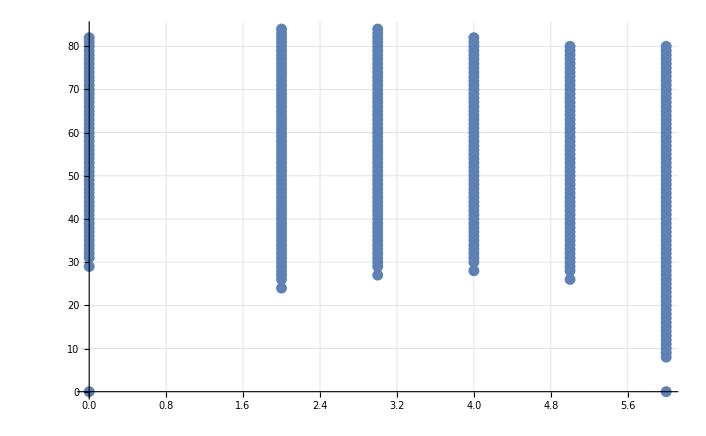

```mathematica
ListPlot[%,GridLines->Automatic]
```

```mathematica
StateSpaceModel={0||13||t>15,0}||{9||t>10,2}||{12||t>13,3}||{13||t>14,4}||{11||t>12,5}||{0||t>7,6};
```

```mathematica
Reduce[-f (-3+1)+(3 b+2 d+3 e)>0&&b>0&&d>0&&e>0&&f>0,Integers]
```

(b|d|e|f)∈Integers&&f≥1&&e≥1&&d≥1&&b≥1

```mathematica
deadbranch[{0,1,0,0,0,0,0}]
(*DeleteDuplicates[Flatten[Map[deadbranch,%],1]]*)
Flatten[Map[deadbranch,%],1];
Flatten[Map[deadbranch,%],1];
Flatten[Map[deadbranch,%],1];
Tally[Flatten[Map[deadbranch,%],1]]
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{4,0,1,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,1,0,0,0,0,0}}

{{{0,0,0,0,0,0,0},99584},{{8,0,1,0,0,0,0},4},{{11,0,0,1,0,0,0},13},{{10,0,1,0,0,0,0},8},{{11,0,1,0,0,0,0},9},{{12,0,0,0,1,0,0},6},{{13,0,0,1,0,0,0},19},{{10,0,0,0,0,1,0},6},{{10,0,0,1,0,0,0},9},{{12,0,1,0,0,0,0},13},{{13,0,1,0,0,0,0},16},{{14,0,0,1,0,0,0},15},{{14,0,1,0,0,0,0},13},{{14,0,0,0,1,0,0},15},{{15,0,0,0,0,0,1},8},{{11,0,0,0,1,0,0},11},{{15,0,0,1,0,0,0},19},{{12,0,0,0,0,1,0},15},{{12,0,0,1,0,0,0},21},{{13,0,0,0,0,0,1},4},{{9,0,0,0,0,1,0},11},{{9,0,0,1,0,0,0},9},{{15,0,1,0,0,0,0},15},{{16,0,0,1,0,0,0},14},{{16,0,1,0,0,0,0},14},{{15,0,0,0,1,0,0},4},{{13,0,0,0,0,1,0},4},{{17,0,0,1,0,0,0},8},{{17,0,1,0,0,0,0},8},{{16,0,0,0,1,0,0},6},{{17,0,0,0,0,0,1},4},{{13,0,0,0,1,0,0},11},{{14,0,0,0,0,0,1},3},{{10,0,0,0,1,0,0},6},{{14,0,0,0,0,1,0},6},{{11,0,0,0,0,1,0},11},{{12,0,0,0,0,0,1},3},{{8,0,0,0,0,1,0},6},{{8,0,0,1,0,0,0},4},{{18,0,0,1,0,0,0},6},{{18,0,1,0,0,0,0},6},{{17,0,0,0,1,0,0},4},{{15,0,0,0,0,1,0},4},{{19,0,0,1,0,0,0},4},{{19,0,1,0,0,0,0},4},{{18,0,0,0,0,0,1},1},{{16,0,0,0,0,0,1},1},{{18,0,0,0,1,0,0},1},{{16,0,0,0,0,1,0},1},{{20,0,0,1,0,0,0},1},{{20,0,1,0,0,0,0},1},{{7,0,1,0,0,0,0},2},{{9,0,1,0,0,0,0},5},{{6,0,1,0,0,0,0},1},{{5,0,1,0,0,0,0},1},{{4,0,1,0,0,0,0},1},{{0,1,0,0,0,0,0},1}}

```mathematica
DeleteDuplicates[Map[Take[#,{2,7}]&,Map[First,{{{10,0,1,0,0,0,0},1},{{13,0,0,1,0,0,0},6},{{12,0,1,0,0,0,0},6},{{13,0,1,0,0,0,0},6},{{14,0,0,0,1,0,0},15},{{15,0,0,1,0,0,0},30},{{12,0,0,0,0,1,0},15},{{14,0,1,0,0,0,0},15},{{15,0,1,0,0,0,0},30},{{16,0,0,1,0,0,0},15},{{16,0,1,0,0,0,0},35},{{16,0,0,0,1,0,0},60},{{17,0,0,0,0,0,1},80},{{17,0,0,1,0,0,0},60},{{14,0,0,0,0,1,0},60},{{15,0,0,0,0,0,1},20},{{17,0,1,0,0,0,0},60},{{18,0,0,1,0,0,0},60},{{18,0,1,0,0,0,0},75},{{17,0,0,0,1,0,0},20},{{15,0,0,0,0,1,0},20},{{19,0,0,1,0,0,0},80},{{19,0,1,0,0,0,0},80},{{18,0,0,0,1,0,0},90},{{19,0,0,0,0,0,1},120},{{16,0,0,0,0,1,0},90},{{20,0,0,1,0,0,0},90},{{20,0,1,0,0,0,0},96},{{19,0,0,0,1,0,0},60},{{17,0,0,0,0,1,0},60},{{21,0,0,1,0,0,0},90},{{21,0,1,0,0,0,0},90},{{20,0,0,0,0,0,1},45},{{18,0,0,0,0,0,1},15},{{20,0,0,0,1,0,0},75},{{18,0,0,0,0,1,0},75},{{22,0,0,1,0,0,0},75},{{22,0,1,0,0,0,0},76},{{21,0,0,0,0,0,1},86},{{21,0,0,0,1,0,0},60},{{19,0,0,0,0,1,0},60},{{23,0,0,1,0,0,0},66},{{23,0,1,0,0,0,0},66},{{22,0,0,0,0,0,1},45},{{22,0,0,0,1,0,0},45},{{20,0,0,0,0,1,0},45},{{24,0,0,1,0,0,0},45},{{24,0,1,0,0,0,0},45},{{23,0,0,0,0,0,1},32},{{23,0,0,0,1,0,0},26},{{21,0,0,0,0,1,0},26},{{25,0,0,1,0,0,0},26},{{25,0,1,0,0,0,0},26},{{24,0,0,0,0,0,1},16},{{24,0,0,0,1,0,0},15},{{22,0,0,0,0,1,0},15},{{26,0,0,1,0,0,0},15},{{26,0,1,0,0,0,0},15},{{25,0,0,0,0,0,1},6},{{25,0,0,0,1,0,0},6},{{23,0,0,0,0,1,0},6},{{27,0,0,1,0,0,0},6},{{27,0,1,0,0,0,0},6},{{26,0,0,0,0,0,1},1},{{26,0,0,0,1,0,0},1},{{24,0,0,0,0,1,0},1},{{28,0,0,1,0,0,0},1},{{28,0,1,0,0,0,0},1}}]]]
```

{{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}

```mathematica
ConstantArray[1,3]
```

{1,1,1}

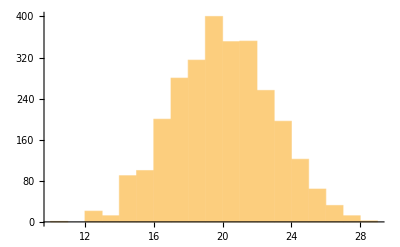

```mathematica
Histogram[Flatten[Map[ConstantArray[First[#[[1]]],#[[2]]]&,{{{10,0,1,0,0,0,0},1},{{13,0,0,1,0,0,0},6},{{12,0,1,0,0,0,0},6},{{13,0,1,0,0,0,0},6},{{14,0,0,0,1,0,0},15},{{15,0,0,1,0,0,0},30},{{12,0,0,0,0,1,0},15},{{14,0,1,0,0,0,0},15},{{15,0,1,0,0,0,0},30},{{16,0,0,1,0,0,0},15},{{16,0,1,0,0,0,0},35},{{16,0,0,0,1,0,0},60},{{17,0,0,0,0,0,1},80},{{17,0,0,1,0,0,0},60},{{14,0,0,0,0,1,0},60},{{15,0,0,0,0,0,1},20},{{17,0,1,0,0,0,0},60},{{18,0,0,1,0,0,0},60},{{18,0,1,0,0,0,0},75},{{17,0,0,0,1,0,0},20},{{15,0,0,0,0,1,0},20},{{19,0,0,1,0,0,0},80},{{19,0,1,0,0,0,0},80},{{18,0,0,0,1,0,0},90},{{19,0,0,0,0,0,1},120},{{16,0,0,0,0,1,0},90},{{20,0,0,1,0,0,0},90},{{20,0,1,0,0,0,0},96},{{19,0,0,0,1,0,0},60},{{17,0,0,0,0,1,0},60},{{21,0,0,1,0,0,0},90},{{21,0,1,0,0,0,0},90},{{20,0,0,0,0,0,1},45},{{18,0,0,0,0,0,1},15},{{20,0,0,0,1,0,0},75},{{18,0,0,0,0,1,0},75},{{22,0,0,1,0,0,0},75},{{22,0,1,0,0,0,0},76},{{21,0,0,0,0,0,1},86},{{21,0,0,0,1,0,0},60},{{19,0,0,0,0,1,0},60},{{23,0,0,1,0,0,0},66},{{23,0,1,0,0,0,0},66},{{22,0,0,0,0,0,1},45},{{22,0,0,0,1,0,0},45},{{20,0,0,0,0,1,0},45},{{24,0,0,1,0,0,0},45},{{24,0,1,0,0,0,0},45},{{23,0,0,0,0,0,1},32},{{23,0,0,0,1,0,0},26},{{21,0,0,0,0,1,0},26},{{25,0,0,1,0,0,0},26},{{25,0,1,0,0,0,0},26},{{24,0,0,0,0,0,1},16},{{24,0,0,0,1,0,0},15},{{22,0,0,0,0,1,0},15},{{26,0,0,1,0,0,0},15},{{26,0,1,0,0,0,0},15},{{25,0,0,0,0,0,1},6},{{25,0,0,0,1,0,0},6},{{23,0,0,0,0,1,0},6},{{27,0,0,1,0,0,0},6},{{27,0,1,0,0,0,0},6},{{26,0,0,0,0,0,1},1},{{26,0,0,0,1,0,0},1},{{24,0,0,0,0,1,0},1},{{28,0,0,1,0,0,0},1},{{28,0,1,0,0,0,0},1}}]]]
```

```mathematica
Total[Map[Last,{{{10,0,1,0,0,0,0},1},{{13,0,0,1,0,0,0},6},{{12,0,1,0,0,0,0},6},{{13,0,1,0,0,0,0},6},{{14,0,0,0,1,0,0},15},{{15,0,0,1,0,0,0},30},{{12,0,0,0,0,1,0},15},{{14,0,1,0,0,0,0},15},{{15,0,1,0,0,0,0},30},{{16,0,0,1,0,0,0},15},{{16,0,1,0,0,0,0},35},{{16,0,0,0,1,0,0},60},{{17,0,0,0,0,0,1},80},{{17,0,0,1,0,0,0},60},{{14,0,0,0,0,1,0},60},{{15,0,0,0,0,0,1},20},{{17,0,1,0,0,0,0},60},{{18,0,0,1,0,0,0},60},{{18,0,1,0,0,0,0},75},{{17,0,0,0,1,0,0},20},{{15,0,0,0,0,1,0},20},{{19,0,0,1,0,0,0},80},{{19,0,1,0,0,0,0},80},{{18,0,0,0,1,0,0},90},{{19,0,0,0,0,0,1},120},{{16,0,0,0,0,1,0},90},{{20,0,0,1,0,0,0},90},{{20,0,1,0,0,0,0},96},{{19,0,0,0,1,0,0},60},{{17,0,0,0,0,1,0},60},{{21,0,0,1,0,0,0},90},{{21,0,1,0,0,0,0},90},{{20,0,0,0,0,0,1},45},{{18,0,0,0,0,0,1},15},{{20,0,0,0,1,0,0},75},{{18,0,0,0,0,1,0},75},{{22,0,0,1,0,0,0},75},{{22,0,1,0,0,0,0},76},{{21,0,0,0,0,0,1},86},{{21,0,0,0,1,0,0},60},{{19,0,0,0,0,1,0},60},{{23,0,0,1,0,0,0},66},{{23,0,1,0,0,0,0},66},{{22,0,0,0,0,0,1},45},{{22,0,0,0,1,0,0},45},{{20,0,0,0,0,1,0},45},{{24,0,0,1,0,0,0},45},{{24,0,1,0,0,0,0},45},{{23,0,0,0,0,0,1},32},{{23,0,0,0,1,0,0},26},{{21,0,0,0,0,1,0},26},{{25,0,0,1,0,0,0},26},{{25,0,1,0,0,0,0},26},{{24,0,0,0,0,0,1},16},{{24,0,0,0,1,0,0},15},{{22,0,0,0,0,1,0},15},{{26,0,0,1,0,0,0},15},{{26,0,1,0,0,0,0},15},{{25,0,0,0,0,0,1},6},{{25,0,0,0,1,0,0},6},{{23,0,0,0,0,1,0},6},{{27,0,0,1,0,0,0},6},{{27,0,1,0,0,0,0},6},{{26,0,0,0,0,0,1},1},{{26,0,0,0,1,0,0},1},{{24,0,0,0,0,1,0},1},{{28,0,0,1,0,0,0},1},{{28,0,1,0,0,0,0},1}}]]
```

2806

```mathematica
Total[Map[Last,Select[{{{10,0,1,0,0,0,0},1},{{13,0,0,1,0,0,0},6},{{12,0,1,0,0,0,0},6},{{13,0,1,0,0,0,0},6},{{14,0,0,0,1,0,0},15},{{15,0,0,1,0,0,0},30},{{12,0,0,0,0,1,0},15},{{14,0,1,0,0,0,0},15},{{15,0,1,0,0,0,0},30},{{16,0,0,1,0,0,0},15},{{16,0,1,0,0,0,0},35},{{16,0,0,0,1,0,0},60},{{17,0,0,0,0,0,1},80},{{17,0,0,1,0,0,0},60},{{14,0,0,0,0,1,0},60},{{15,0,0,0,0,0,1},20},{{17,0,1,0,0,0,0},60},{{18,0,0,1,0,0,0},60},{{18,0,1,0,0,0,0},75},{{17,0,0,0,1,0,0},20},{{15,0,0,0,0,1,0},20},{{19,0,0,1,0,0,0},80},{{19,0,1,0,0,0,0},80},{{18,0,0,0,1,0,0},90},{{19,0,0,0,0,0,1},120},{{16,0,0,0,0,1,0},90},{{20,0,0,1,0,0,0},90},{{20,0,1,0,0,0,0},96},{{19,0,0,0,1,0,0},60},{{17,0,0,0,0,1,0},60},{{21,0,0,1,0,0,0},90},{{21,0,1,0,0,0,0},90},{{20,0,0,0,0,0,1},45},{{18,0,0,0,0,0,1},15},{{20,0,0,0,1,0,0},75},{{18,0,0,0,0,1,0},75},{{22,0,0,1,0,0,0},75},{{22,0,1,0,0,0,0},76},{{21,0,0,0,0,0,1},86},{{21,0,0,0,1,0,0},60},{{19,0,0,0,0,1,0},60},{{23,0,0,1,0,0,0},66},{{23,0,1,0,0,0,0},66},{{22,0,0,0,0,0,1},45},{{22,0,0,0,1,0,0},45},{{20,0,0,0,0,1,0},45},{{24,0,0,1,0,0,0},45},{{24,0,1,0,0,0,0},45},{{23,0,0,0,0,0,1},32},{{23,0,0,0,1,0,0},26},{{21,0,0,0,0,1,0},26},{{25,0,0,1,0,0,0},26},{{25,0,1,0,0,0,0},26},{{24,0,0,0,0,0,1},16},{{24,0,0,0,1,0,0},15},{{22,0,0,0,0,1,0},15},{{26,0,0,1,0,0,0},15},{{26,0,1,0,0,0,0},15},{{25,0,0,0,0,0,1},6},{{25,0,0,0,1,0,0},6},{{23,0,0,0,0,1,0},6},{{27,0,0,1,0,0,0},6},{{27,0,1,0,0,0,0},6},{{26,0,0,0,0,0,1},1},{{26,0,0,0,1,0,0},1},{{24,0,0,0,0,1,0},1},{{28,0,0,1,0,0,0},1},{{28,0,1,0,0,0,0},1}},Last[First[#]]==1&]]]/2806
```

```mathematica
233/1403//N
```

0.166073

```mathematica
branch[{p0_,{a_,b_,c_,d_,e_,f_,g_}}]:=
Select[Block[{sum=a+b+c+d+e+f,list={a,b,c,d,e,f,g}},
{{(a*p)/sum*p0,list+{1,0,0,0,0,0,0}},
{(c*p)/sum*p0,list+{4,0,-1,1,0,0,0}},
{(d*p/3)/sum*p0,list+{2,0,0,-1,1,0,0}},
{(f*p/3)/sum*p0,list+{4,0,0,0,0,-1,1}},
{(a*(1-p))/sum*p0,list+{3,0,0,0,0,0,0}},
{(b*(1-p))/sum*p0,list+{4,-1,1,0,0,0,0}},
{(c*(1-p))/sum*p0,list+{4,0,0,0,0,0,0}},
{(d*(1-p))/sum*p0,list+{0,0,0,-1,0,1,0}},
{(e*(1-p))/sum*p0,list+{4,0,0,0,-1,0,1}},
{(-f (-3+p)+(3 b+2 d+3 e) p)/(3 (sum))*p0,list+{0,0,0,0,0,0,0}}}],¬TrueQ[First[#]==0]&]
```

```mathematica
102 ways in 6 steps
```

```mathematica
branch[{p0_,{a_,b_,c_,d_,e_,f_,g_}}]:=
Select[Block[{sum=a+b+c+d+e+f,list={a,b,c,d,e,f,g}},
{{(a*p)/sum*p0,list+{1,0,0,0,0,0,0}},
{(c*p)/sum*p0,list+{4,0,-1,1,0,0,0}},
{(d*p/3)/sum*p0,list+{2,0,0,-1,1,0,0}},
{(f*p/3)/sum*p0,list+{4,0,0,0,0,-1,1}},
{(a*(1-p))/sum*p0,list+{3,0,0,0,0,0,0}},
{(b*(1-p))/sum*p0,list+{4,-1,1,0,0,0,0}},
{(c*(1-p))/sum*p0,list+{4,0,0,0,0,0,0}},
{(d*(1-p))/sum*p0,list+{0,0,0,-1,0,1,0}},
{(e*(1-p))/sum*p0,list+{4,0,0,0,-1,0,1}},
{(-f (-3+p)+(3 b+2 d+3 e) p)/(3 (sum))*p0,list+{0,0,0,0,0,0,0}}}],¬TrueQ[First[#]==0]&]
```

```mathematica
branchwf[{p0_,{a_,b_,c_,d_,e_,f_,g_}}]:=(*Select[*)Block[{sum=a+b+c+d+e+f,list={a,b,c,d,e,f,g}},Piecewise[{{{p0,{0,0,0,0,0,0,0}}, a==b==c==d==e==f==g==0}, {Select[{{(a*p)/sum*p0,list+{1,0,0,0,0,0,0}},
{(c*p)/sum*p0,list+{4,0,-1,1,0,0,0}},
{(d*p/3)/sum*p0,list+{2,0,0,-1,1,0,0}},
{(f*p/3)/sum*p0,list+{4,0,0,0,0,-1,1}},
{(a*(1-p))/sum*p0,list+{3,0,0,0,0,0,0}},
{(b*(1-p))/sum*p0,list+{4,-1,1,0,0,0,0}},
{(c*(1-p))/sum*p0,list+{4,0,0,0,0,0,0}},
{(d*(1-p))/sum*p0,list+{0,0,0,-1,0,1,0}},
{(e*(1-p))/sum*p0,list+{4,0,0,0,-1,0,1}},
{(-f (-3+p)+(3 b+2 d+3 e) p)/(3 (sum))*p0,{0,0,0,0,0,0,0}}},¬TrueQ[First[#]==0]&], a≠0∨b≠0∨c≠0∨d≠0∨e≠0∨f≠0∨g≠0}}]](*,¬TrueQ[First[#]==0]&]*)
```

```mathematica
branchwf[{p,{0,0,0,0,0,0,0}}]
```

{p,{0,0,0,0,0,0,0}}

```mathematica
Partition[Flatten[Map[branchwf,branchwf[{1,{0,1,0,0,0,0,0}}]]],8]
```

{{4/5 (1-p) p,5,0,1,0,0,0,0},{1/5 (1-p) p,8,0,0,1,0,0,0},{4/5 (1-p)^2,7,0,1,0,0,0,0},{1/5 (1-p)^2,8,0,1,0,0,0,0},{p,0,0,0,0,0,0,0}}

```mathematica
branchlistwf[{{1,{0,1,0,0,0,0,0}}}]
branchwf[{1,{0,1,0,0,0,0,0}}]
Map[{#[[1]],Delete[#,1]}&,Partition[Flatten[%],8]]
branchlistwf[%]
branchlistwf[%]
```

{{1-p,{4,0,1,0,0,0,0}},{p,{0,0,0,0,0,0,0}}}

{{1-p,{4,0,1,0,0,0,0}},{p,{0,0,0,0,0,0,0}}}

{{1-p,{4,0,1,0,0,0,0}},{p,{0,0,0,0,0,0,0}}}

{{4/5 (1-p) p,{5,0,1,0,0,0,0}},{1/5 (1-p) p,{8,0,0,1,0,0,0}},{4/5 (1-p)^2,{7,0,1,0,0,0,0}},{1/5 (1-p)^2,{8,0,1,0,0,0,0}},{p,{0,0,0,0,0,0,0}}}

{{2/3 (1-p) p^2,{6,0,1,0,0,0,0}},{14/45 (1-p) p^2,{9,0,0,1,0,0,0}},{41/30 (1-p)^2 p,{8,0,1,0,0,0,0}},{14/45 (1-p)^2 p,{9,0,1,0,0,0,0}},{1/135 (1-p) p^2,{10,0,0,0,1,0,0}},{5/18 (1-p)^2 p,{11,0,0,1,0,0,0}},{1/45 (1-p)^2 p,{8,0,0,0,0,1,0}},{p+2/135 (1-p) p^2,{0,0,0,0,0,0,0}},{7/10 (1-p)^3,{10,0,1,0,0,0,0}},{5/18 (1-p)^3,{11,0,1,0,0,0,0}},{1/45 (1-p)^2 p,{12,0,0,1,0,0,0}},{1/45 (1-p)^3,{12,0,1,0,0,0,0}}}

```mathematica
pflatten[list_]:=Table[Block[{these=Select[list,Last[#]==i&]},{Total[Map[First,these]],these[[1]][[2]]}],{i,DeleteDuplicates[Map[Last,list]]}]
branch[{1,{0,1,0,0,0,0,0}}]
branchlist[list_]:=pflatten[Flatten[Map[branch,list],1]]
branchlistwf[list_]:=pflatten[Map[{#[[1]],Delete[#,1]}&,Partition[Flatten[Map[branchwf,list]],8]]]
branchlist[{{1,{0,1,0,0,0,0,0}}}]
branchlist[%]
branchlist[%]
branchlist[%]
```

{{1-p,{4,0,1,0,0,0,0}},{p,{0,1,0,0,0,0,0}}}

{{1-p,{4,0,1,0,0,0,0}},{p,{0,1,0,0,0,0,0}}}

{{4/5 (1-p) p,{5,0,1,0,0,0,0}},{1/5 (1-p) p,{8,0,0,1,0,0,0}},{4/5 (1-p)^2,{7,0,1,0,0,0,0}},{1/5 (1-p)^2,{8,0,1,0,0,0,0}},{(1-p) p,{4,0,1,0,0,0,0}},{p^2,{0,1,0,0,0,0,0}}}

{{2/3 (1-p) p^2,{6,0,1,0,0,0,0}},{14/45 (1-p) p^2,{9,0,0,1,0,0,0}},{47/30 (1-p)^2 p,{8,0,1,0,0,0,0}},{14/45 (1-p)^2 p,{9,0,1,0,0,0,0}},{1/135 (1-p) p^2,{10,0,0,0,1,0,0}},{5/18 (1-p)^2 p,{11,0,0,1,0,0,0}},{1/45 (1-p)^2 p,{8,0,0,0,0,1,0}},{29/135 (1-p) p^2,{8,0,0,1,0,0,0}},{7/10 (1-p)^3,{10,0,1,0,0,0,0}},{5/18 (1-p)^3,{11,0,1,0,0,0,0}},{1/45 (1-p)^2 p,{12,0,0,1,0,0,0}},{1/45 (1-p)^3,{12,0,1,0,0,0,0}},{4/5 (1-p) p^2,{5,0,1,0,0,0,0}},{4/5 (1-p)^2 p,{7,0,1,0,0,0,0}},{(1-p) p^2,{4,0,1,0,0,0,0}},{p^3,{0,1,0,0,0,0,0}}}

{{4/5 (1-p)^2 p^2+4/7 (1-p) p^3,{7,0,1,0,0,0,0}},{197/525 (1-p) p^3,{10,0,0,1,0,0,0}},{1982/945 (1-p)^2 p^2,{9,0,1,0,0,0,0}},{7/10 (1-p)^3 p+197/525 (1-p)^2 p^2,{10,0,1,0,0,0,0}},{(127 (1-p) p^3)/7425,{11,0,0,0,1,0,0}},{(49831 (1-p)^2 p^2)/70200,{12,0,0,1,0,0,0}},{(103 (1-p)^2 p^2)/2025,{9,0,0,0,0,1,0}},{(2096 (1-p) p^3)/6075,{9,0,0,1,0,0,0}},{(6323 (1-p)^3 p)/2970,{11,0,1,0,0,0,0}},{(3827 (1-p)^3 p)/5400,{12,0,1,0,0,0,0}},{(151 (1-p)^2 p^2)/2925,{13,0,0,1,0,0,0}},{7/11 (1-p)^4+(151 (1-p)^3 p)/2925,{13,0,1,0,0,0,0}},{(103 (1-p)^2 p^2)/7128,{13,0,0,0,1,0,0}},{((1-p)^2 p^2)/1485,{14,0,0,0,0,0,1}},{(346 (1-p) p^3)/40095,{10,0,0,0,1,0,0}},{(3781 (1-p)^3 p)/11880,{14,0,0,1,0,0,0}},{(139 (1-p)^3 p)/3240,{11,0,0,0,0,1,0}},{(1489 (1-p)^2 p^2)/4860,{11,0,0,1,0,0,0}},{((1-p)^2 p^2)/1215,{12,0,0,0,0,0,1}},{((1-p)^2 (3-p) p)/1215+(29 (1-p)^2 p^2)/1215,{8,0,0,0,0,1,0}},{(787 (1-p) p^3)/3645,{8,0,0,1,0,0,0}},{(3781 (1-p)^4)/11880,{14,0,1,0,0,0,0}},{(613 (1-p)^3 p)/14040,{15,0,0,1,0,0,0}},{(613 (1-p)^4)/14040,{15,0,1,0,0,0,0}},{((1-p)^2 p^2)/1755,{14,0,0,0,1,0,0}},{1/585 (1-p)^3 p,{12,0,0,0,0,1,0}},{1/585 (1-p)^3 p,{16,0,0,1,0,0,0}},{1/585 (1-p)^4,{16,0,1,0,0,0,0}},{2/3 (1-p) p^3,{6,0,1,0,0,0,0}},{47/30 (1-p)^2 p^2,{8,0,1,0,0,0,0}},{4/5 (1-p) p^3,{5,0,1,0,0,0,0}},{(1-p) p^3,{4,0,1,0,0,0,0}},{p^4,{0,1,0,0,0,0,0}}}

```mathematica
Total[Map[First,Select[Nest[branchlistwf,{{1,{0,1,0,0,0,0,0}}},4],Last[Last[#]]≠0&]]]
```

First::normal: Nonatomic expression expected at position 1 in First[p].

Last::normal: Nonatomic expression expected at position 1 in Last[p].

General::stop: Further output of Last :: normal will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[p].

Part::partd: Part specification p ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 2 of branchwf[{First[p], p ⟦ 2 ⟧}] does not exist.

Part::partw: Part 2 of branchwf[{{First[p], p ⟦ 2 ⟧}, branchwf[{First[p], p ⟦ 2 ⟧}] ⟦ 2 ⟧}] does not exist.

{{(4 (1-p)^2 p^2)/2673+First[p],(4 (1-p)^2 p^2)/2673+p⟦2⟧},(4 (1-p)^2 p^2)/2673+branchwf[{First[p],p⟦2⟧}]⟦2⟧}

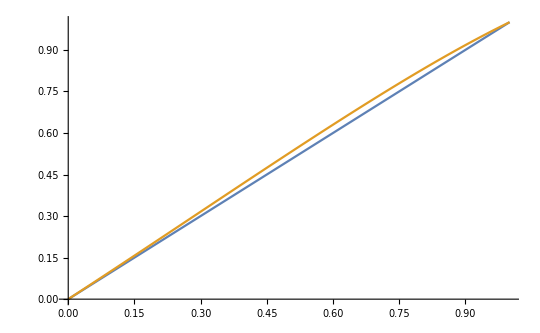

```mathematica
Total[Map[First,Select[Nest[branchlistwf,{{1,{0,1,0,0,0,0,0}}},12],Last[#]=={0,0,0,0,0,0,0}&]]];
Plot[{p,%},{p,0,1}]
```

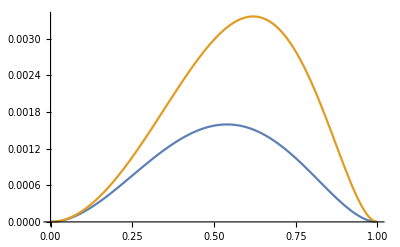

```mathematica
{Total[Map[First,Select[Nest[branchlistwf,{{1,{0,1,0,0,0,0,0}}},10],Last[Last[#]]≠0&]]],Total[Map[First,Select[Nest[branchlist,{{1,{0,1,0,0,0,0,0}}},10],Last[Last[#]]≠0&]]]};
Plot[%,{p,0,1}]
```

```mathematica
p=1/2;
Total[Map[First,Select[Nest[branchlist,{{1,{0,1,0,0,0,0,0}}},80],Last[Last[#]]≠0&]]]
N[%]
1/%
Clear[p]
```

0.0396602

25.2142

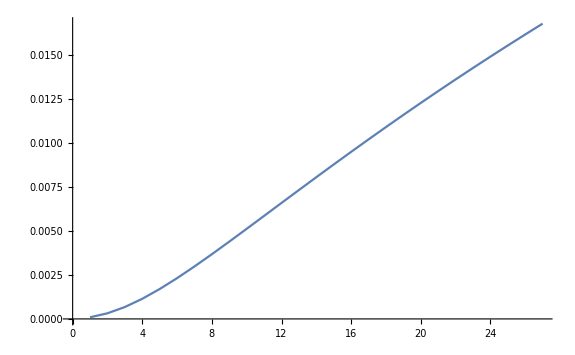

0.0168076

59.497

```mathematica
p=1/2;
Monitor[Table[Total[Map[First,Select[Nest[branchlist,{{1,{0,1,0,0,0,0,0}}},c],Last[Last[#]]≠0&]]],{c,4,30}],c]
ListPlot[%,Joined->True]
Clear[p]
```

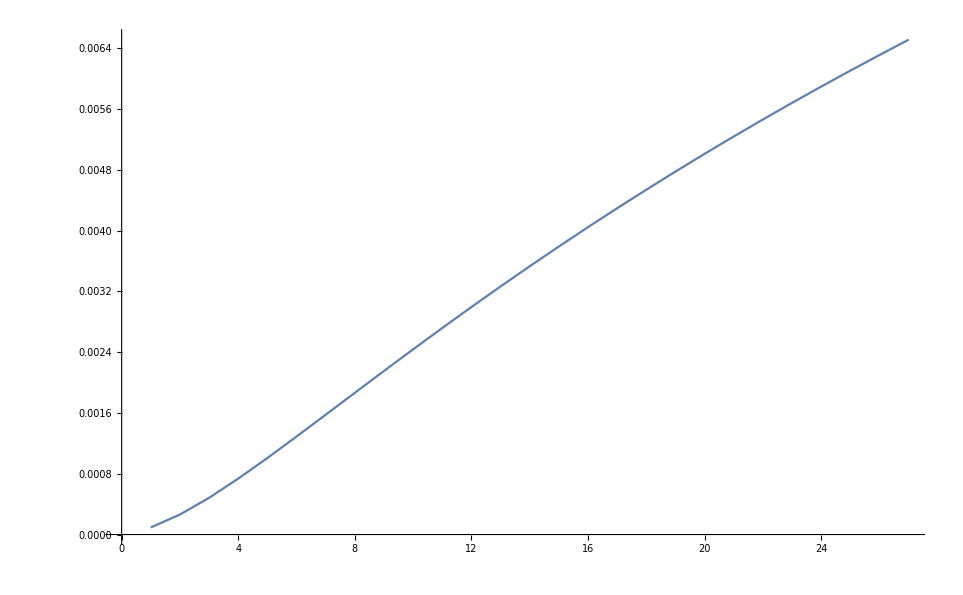

```mathematica
p=1/2;
Monitor[Table[Total[Map[First,Select[Nest[branchlistwf,{{1,{0,1,0,0,0,0,0}}},c],Last[Last[#]]≠0&]]],{c,4,30}],c]
ListPlot[%,Joined->True]
Clear[p]
```

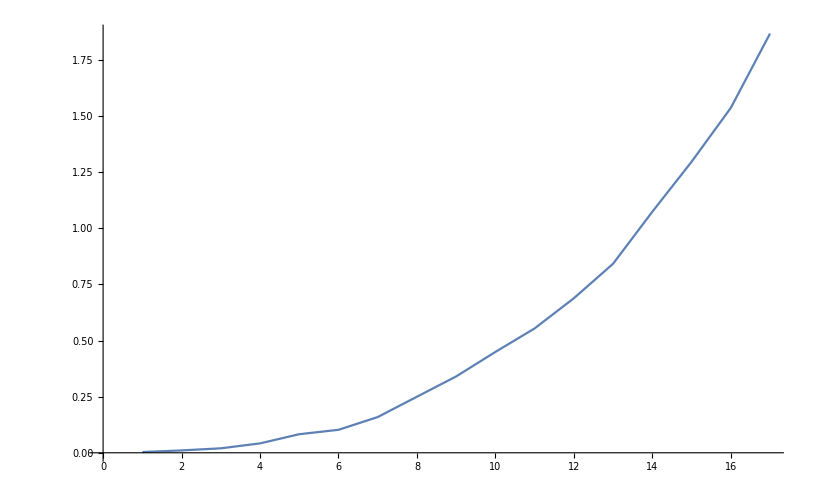

```mathematica
{0.00328500000000000015945578191178810812`3.5371352871754236,0.0105009999999999999176214515728133847`4.041830571759327,0.01983800000000000146593848171505669598`4.318097799205322,0.04184700000000000225108820472996740136`4.642264242272074,0.08270600000000000173727698893344495445`4.938136930357806,0.10229800000000000004263256414560601115`5.030467056303079,0.15908200000000000118305365504056680948`5.2222209556357075,0.24965899999999999203659228896867716685`5.417947139909024,0.34004899999999999016253582340141292661`5.55214141531105,0.44915500000000002644995333866972941905`5.672996151896084,0.55392099999999999671018713343073613942`5.764047743512493,0.68831900000000001416111672369879670441`5.85838967103802,0.84199199999999996268940094523713923991`5.945907878446304,1.07357900000000006102141014707740396261`6.051433921066056,1.29608300000000009610801043891115114093`6.133232727536253,1.53606700000000007122480383259244263172`6.2070100723967885,1.86699900000000007516121058870339766145`6.2917439986124215}
```

```mathematica
Total[Map[First,Select[Nest[branchlist,{{1,{0,1,0,0,0,0,0}}},4],Last[Last[#]]≠0&]]]
```

(4 (1-p)^2 p^2)/2673

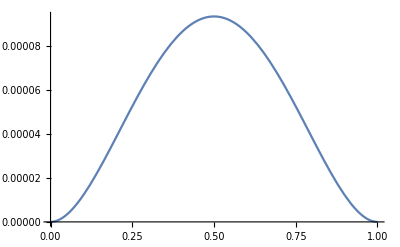

```mathematica
Plot[(4 (1-p)^2 p^2)/2673,{p,0,1}]
```

```mathematica
Solve[D[(4 (1-p)^2 p^2)/2673,p]==0&&0≤p≤1]
```

{{p→0},{p→1/2},{p→1}}

```mathematica
∫_0^1 Total[Map[First,Select[Nest[branchlist,{{1,{0,1,0,0,0,0,0}}},10],Last[Last[#]]≠0&]]]ⅆp
N[%]
```

680379018265749736440424525118077253603246196273631739447619126102726293/393664897883680103066966499904252764460450456316040540277403811840000000000

0.00172832

```mathematica
Total[Map[First,Select[Nest[branchlist,{{1,{0,1,0,0,0,0,0}}},5],Last[Last[#]]≠0&]]]
```

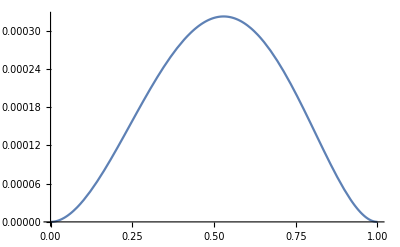

```mathematica
Plot[(28854913 (1-p)^3 p^2)/7589181600+(238243 (1-p)^2 p^3)/44104500+1/27 p (((1-p)^2 (3-p) p)/1215+(29 (1-p)^2 p^2)/1215),{p,0,1}]
```

```mathematica
Expand[(28854913 (1-p)^3 p^2)/7589181600+(238243 (1-p)^2 p^3)/44104500+1/27 p (((1-p)^2 (3-p) p)/1215+(29 (1-p)^2 p^2)/1215)]
```

(88646819 p^2)/22767544800-(20037643237 p^3)/3756644892000-(3804888931 p^4)/3756644892000+(9215807033 p^5)/3756644892000

```mathematica
Solve[D[(28854913 (1-p)^3 p^2)/7589181600+(238243 (1-p)^2 p^3)/44104500+1/27 p (((1-p)^2 (3-p) p)/1215+(29 (1-p)^2 p^2)/1215),p]==0&&0≤p≤1]
```

{{p→0},{p→1},{p→(-30859479441+√6344190526125136650681)/92158070330}}

{4.69369,(130371570685577165117185988567 (1-p)^11 p^2)/3200343694102079257004828974425047040000+130+1/20 (1-p) (1/20 p (18/19 p (1)+1/20 p (1/20 p (1/20 p ((6737502715786261871 (1-p)^3 p^5)/31825704445831296000+1+1+16/17 (1-p) ((321482737 (1-p)^2 p^5)/3497894400+1/17 p (1)+1+13/14 (1-p) ((947367511 (1-p)^2 p^4)/102696446160+(16871 (1-p) p^5)/675675+1/36 p ((10967 (1-p)^2 p^3)/52488+(394 (1-p) p^4)/1155+1/8 p (4/5 (1-p)^2 p^2+4/7 (1-p) p^3)))))+2+1)+2+1)+1+16/17 (1-p) (1))+2+1)}
 |  |  |  |

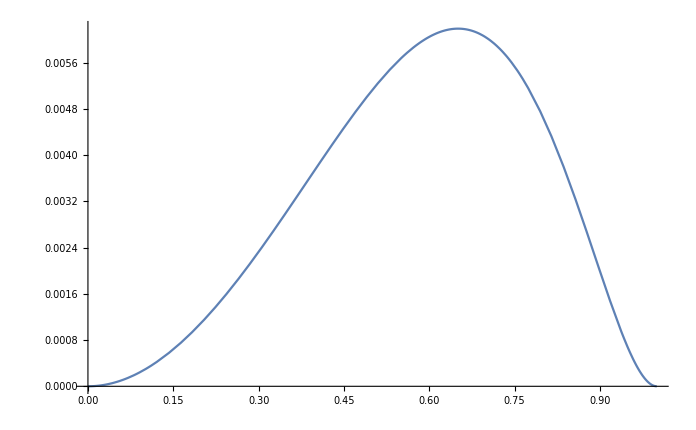
{4.69369,-Graphics-}

```mathematica
Timing[Total[Map[First,Select[Nest[branchlist,{{1,{0,1,0,0,0,0,0}}},13],Last[Last[#]]≠0&]]]]
{%[[1]],Plot[%[[2]],{p,0,1}]}
```

```mathematica
NMaximize[{Out[14][[2]],0<p<1},p]
```

$Aborted

```mathematica
Join[Table[Total[Map[First,Select[Nest[branchlist,{{1,{0,1,0,0,0,0,0}}},j],Last[Last[#]]≠0&]]],{j,4,8}],Table[Total[Map[First,Select[Nest[branchlistwf,{{1,{0,1,0,0,0,0,0}}},j],Last[Last[#]]≠0&]]],{j,4,8}]]
```

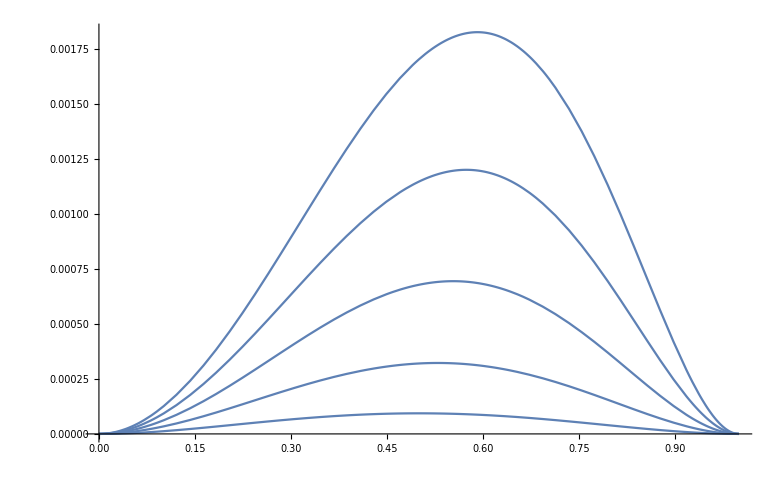

```mathematica
Monitor[Plot[Table[Total[Map[First,Select[Nest[branchlist,{{1,{0,1,0,0,0,0,0}}},j],Last[Last[#]]≠0&]]],{j,4,8}],{p,0,1}],{j,Graphics[{Line[{{0,0},{1,0}}],Point[{p,0}]}]}]
```

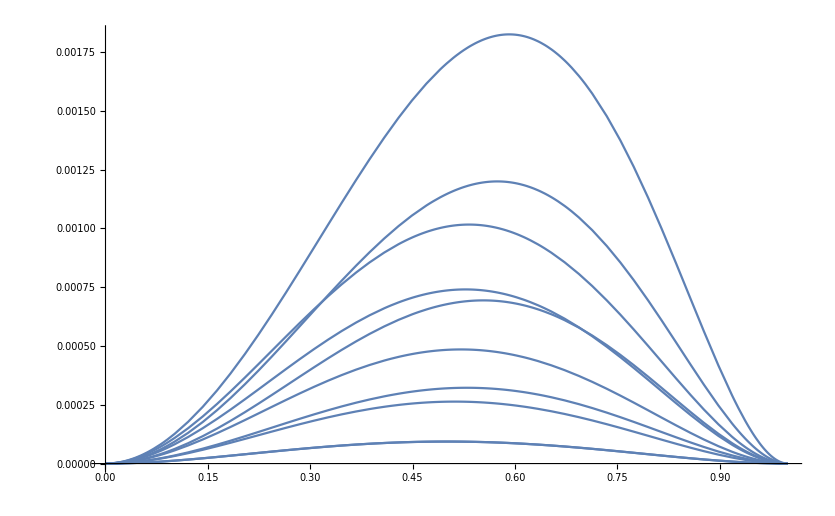

```mathematica
Monitor[Plot[Join[Table[Total[Map[First,Select[Nest[branchlist,{{1,{0,1,0,0,0,0,0}}},j],Last[Last[#]]≠0&]]],{j,4,8}],Table[Total[Map[First,Select[Nest[branchlistwf,{{1,{0,1,0,0,0,0,0}}},j],Last[Last[#]]≠0&]]],{j,4,8}]],{p,0,1}],{j,Graphics[{Line[{{0,0},{1,0}}],Point[{p,0}]}]}]
```